# 三点画圆

```mathematica
pts=RandomReal[3,{3,2}]
```

{{0.174611,1.7197},{1.2044,1.64921},{2.75631,2.19113}}

### 方式一

```mathematica
Circumsphere[pts]
```

Sphere[{0.914585,4.97223},3.33564]

```mathematica
RegionMember[Circumsphere[pts],{x,y}]
```

(x|y)∈ℝ&&(-0.914585+x)^2+(-4.97223+y)^2==11.1265

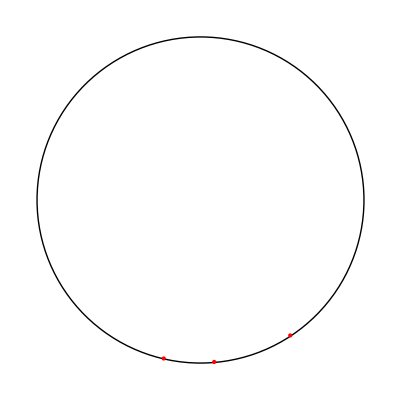

```mathematica
Graphics[{Circumsphere[pts],Red,PointSize[Large],Point[pts]}]
```

### 方式二

{{x→-0.490076,y→-0.0920344}}

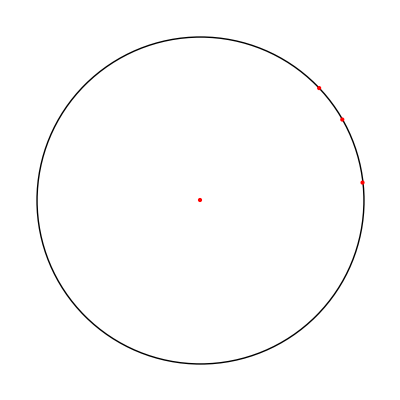

```mathematica
(*版本10前解法*)
dis=Total[({x,y}-#)^2]&;
{center}=Solve[Equal@@dis/@pts,{x,y},Reals]
Graphics[{Circle[{x,y},Sqrt@dis@pts[[1]]],Red,PointSize@Medium,Point[pts~Join~{{x,y}}]}/. center]
```

### 方式三

计算三角形的外心

```mathematica
center3=TriangleCenter[pts,"Circumcenter"]
```

{-0.490076,-0.0920344}

```mathematica
r3=Norm[pts[[1]]-center3]
```

1.3782

```mathematica
Graphics[{Circle[center3,r3],Red,PointSize[Large],Point@pts,Point@center3}]
```

-Graphics-